# 解析几何求解器

## 构造

### 点和坐标系

#### point[x, y] Coord[x,y],$x, $y

```mathematica
point[p__][i_]:=point[p][[i]];
point[p__]["X"]:=point[p][[1]];
point[p__]["Y"]:=point[p][[2]];
point[p_List]:=point@@p;

point/:a_*point[x_,y_]:=point[a x,a y];
point/:point[x1_,y1_]+point[x2_,y2_]:=point[x1+x2,y1+y2];
```

```mathematica
coord[x_Symbol,y_Symbol]:=(Unprotect[x,y,$x,$y];ClearAll[x,y,$x,$y];$x=x;$y=y;Protect[x,y,$x,$y];);
```

#### 解释器

```mathematica
point/:MakeBoxes[obj:point[x_,y_],form:(StandardForm|TraditionalForm)]:=Module[{above,below},
above={{BoxForm`SummaryItem[{Short[{x,y}]}],SpanFromLeft}};
below={{BoxForm`SummaryItem[{"横坐标: ",x}],SpanFromLeft},
{BoxForm`SummaryItem[{"纵坐标: ",y}],SpanFromLeft}};
BoxForm`ArrangeSummaryBox[
"point",(*显示的对象名称,请使用字符型以避免上下文问题*)
obj,(*数据,不要动*)
Graphics[{Point[{0,0}]},ImageSize->20],(*图标,没有填None*)
above,(*显示的属性,不要动*)
below,(*按加号之后显示的属性,不要动*)
form,(*需要渲染的格式,不要动*)
"Interpretable"->Automatic]];
```

#### 中点

```mathematica
midpoint[p1_point,p2_point]:=point[(p1[1]+p2[1])/2,(p1[2]+p2[2])/2];
midpoint[a_List]:=midpoint@@a;
```

N分点, 向量 AC=n BC

```mathematica
nthpoint[p1_point,p2_point,n_]:=point[(p1[1]-n p2[1])/(1-n),(p1[2]-n p2[2])/(1-n)];
```

#### 三点共线

```mathematica
online[p1_point,p2_point,p3_point]:=Det[{#⟦1⟧,#⟦2⟧,1}&/@{p1,p2,p3}]//Simplify;
onlineQ[p1_point,p2_point,p3_point]:=online[p1,p2,p3]==0;
onlineQQ[p1_point,p2_point,p3_point]:=Simplify[online[p1,p2,p3]]===0;
```

### 向量，角平分线

#### 向量 arrow[x,y]

```mathematica
arrow[p__][i_Integer]:=arrow[p][[i]];
arrow[p__]["X"]:=arrow[p][[1]];
arrow[p__]["Y"]:=arrow[p][[2]];


arrow[p1_point,p2_point]:=arrow[p2[1]-p1[1],p2[2]-p1[2]];
arrow[p:(_point|_List)]:=arrow@@p;
arrow/:a_*arrow[x_,y_]/;And@@(Head[#]=!=point&/@{x,y}):=arrow[a x,a y];
arrow/:arrow[x1_,y1_]+arrow[x2_,y2_]/;And@@(Head[#]=!=point&/@{x1,y1,x2,y2}):=arrow[x1+x2,y1+y2];
arrow/:arrow[p1__].arrow[p2__]:={p1}.{p2};
arrow/:point[p__]+arrow[a__]:=point[{p}+{a}];
point[a_arrow]:=point@@a;


verticalarrow[a_arrow]:=arrow[a[2],-a[1]];
```

```mathematica
verticalQ[a_arrow,b_arrow]:=Simplify[a.b]==0;
verticalQQ[a_arrow,b_arrow]:=Simplify[a.b]===0;
parallelQ[a_arrow,b_arrow]:=Simplify[b[1]a[2]-b[2]a[1]]==0;
parallelQQ[a_arrow,b_arrow]:=Simplify[b[1]a[2]-b[2]a[1]]===0;
```

#### 解释器

```mathematica
arrow/:MakeBoxes[obj:arrow[x_,y_],form:(StandardForm|TraditionalForm)]:=Module[{above,below},
above={{BoxForm`SummaryItem[{Short[{x,y}]}],SpanFromLeft}};
below={{BoxForm`SummaryItem[{"横坐标: ",x}],SpanFromLeft},
{BoxForm`SummaryItem[{"纵坐标: ",y}],SpanFromLeft}};
BoxForm`ArrangeSummaryBox[
"arrow",(*显示的对象名称,请使用字符型以避免上下文问题*)
obj,(*数据,不要动*)
Graphics[{Arrowheads[0.3],Arrow[{{1,0},{2,1}}]},ImageSize->20],(*图标,没有填None*)
above,(*显示的属性,不要动*)
below,(*按加号之后显示的属性,不要动*)
form,(*需要渲染的格式,不要动*)
"Interpretable"->Automatic]];
```

#### 向量模

```mathematica
norm[a_arrow]:=√(a.a);
```

#### 向量夹角

```mathematica
cosangle[a_arrow,b_arrow]:=(a.b)/(norm[a]norm[b])//Simplify;
```

#### 角平分线向量：

```mathematica
midangle[arrow[x1_,y1_],arrow[x2_,y2_]]:=arrow[x2 √(x1^2+y1^2)+x1 √(x2^2+y2^2),√(x1^2+y1^2) y2+y1 √(x2^2+y2^2)]//Simplify
```

### 线

#### line[A, B, C, exp]

```mathematica
line[l__][i_Integer]:=line[l][[i]];
line[l__]["A"]:=line[l][[1]];
line[l__]["B"]:=line[l][[2]];
line[l__]["C"]:=line[l][[3]];
line[l__]["exp"]:=line[l][[4]];
```

危险：

```mathematica
line[A_,B_,C_]:=Module[{a,b,c},{a,b,c}={A,B,C}//Simplify;line[a,b,c,a $x+b $y+c]];
line/:a_*line[A_,B_,C_,exp_]:=line[a A,a B,a C,a exp];
line/:line[A1_,B1_,C1_,__]+line[A2_,B2_,C2_,__]:=line[A1+A2,B1+B2,C1+C2];
```

```mathematica
line[p1_point,p2_point]:=
Module[{exp,aa,bb,cc},
exp=Collect[Det[{#⟦1⟧,#⟦2⟧,1}&/@{{$x,$y},p1,p2}],{$x,$y}];
aa=Coefficient[exp,$x,1]//Together//Simplify;bb=Coefficient[exp,$y,1]//Together//Simplify;
cc=Coefficient[Coefficient[exp,$x,0],$y,0]//Together//Simplify;
line[aa,bb,cc,aa $x+bb $y+cc]];
```

方向加过定点：

```mathematica
line[p_point,{dx_,dy_}]:=line[dy,-dx, dx p[2]-dy p[1]//Together//Simplify,dy $x-dx $y +dx p[2]-dy p[1]//Together//Simplify];
line[p_point,a_arrow]:=line[p,List@@a];
line[a_arrow,p_point]:=line[p,a];
```

#### 解释器

```mathematica
line/:MakeBoxes[obj:line[a_,b_,c_,exp_],form:(StandardForm|TraditionalForm)]:=Module[{above,below},
above={{BoxForm`SummaryItem[{Short[exp==0]}],SpanFromLeft}};
below={{BoxForm`SummaryItem[{"A: ",a}],SpanFromLeft},
{BoxForm`SummaryItem[{"B: ",b}],SpanFromLeft},
{BoxForm`SummaryItem[{"C: ",c}],SpanFromLeft},
{BoxForm`SummaryItem[{"exp: ",exp}],SpanFromLeft}};
BoxForm`ArrangeSummaryBox[
"line",(*显示的对象名称,请使用字符型以避免上下文问题*)
obj,(*数据,不要动*)
Graphics[{Line[{{1,0},{2,1}}]},ImageSize->20],(*图标,没有填None*)
above,(*显示的属性,不要动*)
below,(*按加号之后显示的属性,不要动*)
form,(*需要渲染的格式,不要动*)
"Interpretable"->Automatic]];
```

#### 平行，重合和垂直

平行，重合和垂直

```mathematica
sameline[l1_line,l2_line]:={Simplify[l1[2]l2[1]-l1[1]l2[2]],Simplify[l1[2]l2[3]-l1[3]l2[2]]};
```

```mathematica
sameQ[l1_line,l2_line]:=And[Simplify[l1[2]l2[1]-l1[1]l2[2]]==0,Simplify[l1[2]l2[3]-l1[3]l2[2]]==0];
sameQQ[l1_line,l2_line]:=And[Simplify[l1[2]l2[1]-l1[1]l2[2]]===0,Simplify[l1[2]l2[3]-l1[3]l2[2]]===0];
parallelQ[l1_line,l2_line]:=And[Simplify[l1[2]l2[1]-l1[1]l2[2]]==0,Simplify[l1[2]l2[3]-l1[3]l2[2]]≠0];
parallelQQ[l1_line,l2_line]:=And[Simplify[l1[2]l2[1]-l1[1]l2[2]]===0,Simplify[l1[2]l2[3]-l1[3]l2[2]]=!=0];
verticalQ[l1_line,l2_line]:=Simplify[l1[1]l2[1]+l1[2]l2[2]]==0
verticalQQ[l1_line,l2_line]:=Simplify[l1[1]l2[1]+l1[2]l2[2]]===0
```

#### 垂直线

垂直线

```mathematica
verticalline[p_point,l_line]:=line[p,{l[1],l[2]}];
verticalline[l_line,p_point]:=verticalline[p,l];

verticalline[p_point,a_arrow]:=line[p,verticalarrow@a];
verticalline[a_arrow,p_point]:=verticalline[p,a];
```

垂直平分线

```mathematica
midverticalline[p1_point,p2_point]:=verticalline[midpoint[p1,p2],line[p1,p2]]
```

垂足

```mathematica
verticalpoint[p_point,l_line]:=intersectpoint[l,verticalline[p,l]];
verticalpoint[l_line,p_point]:=verticalpoint[p,l];
```

#### 三线共点

```mathematica
onpoint[l1_line,l2_line,l3_line]:=Det[{#[1],#[2],#[3]}&/@{l1,l2,l3}]//Simplify;
onpointQ[l1_line,l2_line,l3_line]:=onpoint[l1,l2,l3]==0;
onpointQQ[l1_line,l2_line,l3_line]:=onpoint[l1,l2,l3]===0;
```

#### 点在线上

```mathematica
online[p_point,l_line]:=Simplify[p[1]l[1]+p[2]l[2]+l[3]];
online[l_line,p_point]:=online[p,l];

onlineQ[p_,l_]:=online[p,l]==0;
onlineQQ[p_,l_]:=online[p,l]===0;
```

#### 线的方向

```mathematica
arrow[l_line]:=arrow[l[2],-l[1]];
```

#### 线的平移

```mathematica
arrow/:arrow[x_,y_]+l_line:=line[l[1],l[2],-x l[1]-y l[2]+l[3]];
```

### 圆

#### circle[{a, b}, r, D, E, F, exp]

circle[{a, b}, r, D, E, F, exp]

```mathematica
circle[c__][i_Integer]/;i≠1:=circle[c][[i]];
circle[c__][1]:=point@@circle[c][[1]];

circle[c__]["D"]:=circle[c][[3]];
circle[c__]["E"]:=circle[c][[4]];
circle[c__]["F"]:=circle[c][[5]];
circle[c__]["exp"]:=circle[c][[-1]];
circle[c__]["r"]:=circle[c][[2]];
circle[c__]["o"]:=circle[c][[1]];
```

圆心和半径，三点

```mathematica
circle[p_point,r_]:=Module[{dd=-2p[1],ee=-2p[2],ff=p[1]^2+p[2]^2-r^2},
circle[List@@p,r,dd,ee,ff,($x)^2+($y)^2+dd $x+ee $y+ff]];
circle[r_]:=circle[point[0,0],r];

circle[p1_point,p2_point,p3_point]:=Module[{dd,ee,ff,exp},
exp=Det[{#⟦1⟧^2+#⟦2⟧^2,#⟦1⟧,#⟦2⟧,1}&/@{{$x,$y},p1,p2,p3}];
dd=Coefficient[exp,$x,1]/Coefficient[exp,$x,2]//Together//Simplify;
ee=Coefficient[exp,$y,1]/Coefficient[exp,$y,2]//Together//Simplify;
ff=Coefficient[Coefficient[exp,$x,0],$y,0]/Coefficient[exp,$x,2]//Together//Simplify;
circle[{-dd/2,-ee/2},√(dd^2+ee^2-4ff)/2//Simplify,dd,ee,ff,$x^2+$y^2+dd $x+ee $y+ff]]
```

AB为直径的圆

```mathematica
circle[a_point,b_point]:=circle[midpoint[a,b],distant[a,b]/2];
```

DEF

```mathematica
circle[{D_,E_,F_}]:=circle[{-D/2,-E/2},√(D^2+E^2-4F)/2//Simplify,D,E,F,$x^2+$y^2+D $x+E $y+F];
```

#### 解释器

```mathematica
circle/:MakeBoxes[obj:circle[{a_,b_},r_,d_,e_,f_,exp_],form:(StandardForm|TraditionalForm)]:=Module[{above,below},
above={{BoxForm`SummaryItem[{"圆心: ",Short[{a,b}]}],SpanFromLeft},
{BoxForm`SummaryItem[{"半径: ",Short[r]}],SpanFromLeft}};
below={
{BoxForm`SummaryItem[{"D: ",d}],SpanFromLeft},
{BoxForm`SummaryItem[{"E: ",e}],SpanFromLeft},
{BoxForm`SummaryItem[{"F: ",f}],SpanFromLeft},
{BoxForm`SummaryItem[{"exp: ",exp}],SpanFromLeft},
{BoxForm`SummaryItem[{"圆心: ",{a,b}}],SpanFromLeft},
{BoxForm`SummaryItem[{"半径: ",r}],SpanFromLeft}
};
BoxForm`ArrangeSummaryBox[
"circle",(*显示的对象名称,请使用字符型以避免上下文问题*)
obj,(*数据,不要动*)
Graphics[Circle[],ImageSize->20],(*图标,没有填None*)
above,(*显示的属性,不要动*)
below,(*按加号之后显示的属性,不要动*)
form,(*需要渲染的格式,不要动*)
"Interpretable"->Automatic]];
```

#### 点和圆的关系

```mathematica
oncircle[p_point,c_circle]:=distantSq[p,point@@c[1]]-c[2]^2//Simplify;
oncircle[c_circle,p_point]:=oncircle[p,c];
```

```mathematica
oncircleQ[p_,c_]:=oncircle[p,c]==0;
oncircleQQ[p_,c_]:=oncircle[p,c]===0;

incircleQ[p_,c_]:=oncircle[p,c]<0;
outcircleQ[p_,c_]:=oncircle[p,c]>0;
```

#### 四点共圆

```mathematica
oncircle[p1_point,p2_point,p3_point,p4_point]:=Det[{#⟦1⟧^2+#⟦2⟧^2,#⟦1⟧,#⟦2⟧,1}&/@{p1,p2,p3,p4}];
oncircleQ[p1_point,p2_point,p3_point,p4_point]:=Simplify[oncircle[p1,p2,p3,p4]]==0;
oncircleQQ[p1_point,p2_point,p3_point,p4_point]:=Simplify[oncircle[p1,p2,p3,p4]]===0;
```

#### Great line: 圆外一点做二切线，切点弦的直线

```mathematica
greatline[p_point,c_circle]:=line[p[1]+c[3]/2,p[2]+c[4]/2,(p[1]c[3]+p[2]c[4]+2c[5])/2];
greatline[c_circle,p_point]:=greatline[p,c];
```

#### 切点

```mathematica
tangentpoint[p_point,c_circle]:=intersectpoint[greatline[p,c],c];
tangentpoint[c_circle,p_point]:=tangentpoint[p,c];
```

#### 切线

```mathematica
tangentline[p_point,c_circle,0]:={};
tangentline[p_point,c_circle,1]:=line[p,{#[[2]],-#[[1]]}&@arrow[p,point@@c[1]]]//Simplify;
tangentline[p_point,c_circle,2]:=tangentline[#,c,0]&/@tangentpoint[p,c];
tangentline[c_circle,p_point,i___]:=tangentline[p,c,i];

tangentline[p_point,c_circle]:=Block[{cons},cons=oncircle[p,c];
Which[cons==0,tangentline[p,c,1],cons>1,tangentline[p,c,2],cons<1,{}]];
```

```mathematica
tangentQ[l_line,c_circle]:=distantSq[c[1],l]==c[2]^2;
```

#### 根轴，根心

```mathematica
radicalaxis[c1_circle,c2_circle]:=line[c1[3]-c2[3],c1[4]-c2[4],c1[5]-c2[5]];
```

```mathematica
radicalroot[c1_circle,c2_circle,c3_circle]:=intersectpoint[radicalaxis[c1,c2],radicalaxis[c1,c3]];
```

#### 圆的平移

```mathematica
arrow/: a_arrow+c_circle:=circle[c[1]+a,c[2]];
```

#### 两圆关系

```mathematica
out[c1_circle,c2_circle]:=distantSq[c1[1],c2[1]]-(c1[2]+c2[2])^2//Simplify;
in[c1_circle,c2_circle]:=distantSq[c1[1],c2[1]]-(c1[2]-c2[2])^2//Simplify;

outQ[c1_circle,c2_circle]:=out[c1,c2]>0;
outtangentQ[c1_circle,c2_circle]:=out[c1,c2]==0;
intersectQ[c1_circle,c2_circle]:=And[out[c1,c2]<0,in[c1,c2]>0];
intangentQ[c1_circle,c2_circle]:=in[c1,c2]==0;
inQ[c1_circle,c2_circle]:=in[c1,c2]<0;
```

#### 两圆公切线

```mathematica
tangentline[circle[{a1_,b1_},r1_,__],circle[{a2_,b2_},r2_,__],4]:=
{line[(b1-b2) (a2 b1-a1 b2)-(r1-r2) (a2 r1-a1 r2)+(b2 r1-b1 r2)√((a1-a2)^2+(b1-b2)^2-(r1-r2)^2) ,(-a1+a2) (a2 b1-a1 b2)-(r1-r2) (b2 r1-b1 r2)+(-a2 r1+a1 r2) √((a1-a2)^2+(b1-b2)^2-(r1-r2)^2) ,(a2 r1-a1 r2)^2+(b2 r1-b1 r2)^2-(a2 b1-a1 b2)^2],
line[(b1-b2) (a2 b1-a1 b2)-(r1-r2) (a2 r1-a1 r2)-(b2 r1-b1 r2)√((a1-a2)^2+(b1-b2)^2-(r1-r2)^2) ,(-a1+a2) (a2 b1-a1 b2)-(r1-r2) (b2 r1-b1 r2)-(-a2 r1+a1 r2) √((a1-a2)^2+(b1-b2)^2-(r1-r2)^2) ,(a2 r1-a1 r2)^2+(b2 r1-b1 r2)^2-(a2 b1-a1 b2)^2],line[(b1-b2) (a2 b1-a1 b2)-(r1+r2) (a2 r1+a1 r2)+(b2 r1+b1 r2)√((a1-a2)^2+(b1-b2)^2-(r1+r2)^2) ,-((a1-a2) (a2 b1-a1 b2)+(r1+r2) (b2 r1+b1 r2)+(a2 r1+a1 r2) √((a1-a2)^2+(b1-b2)^2-(r1+r2)^2) ),(a2 r1+a1 r2)^2+(b2 r1+ b1 r2)^2-(a2 b1-a1 b2)^2],
line[(b1-b2) (a2 b1-a1 b2)-(r1+r2) (a2 r1+a1 r2)-(b2 r1+b1 r2)√((a1-a2)^2+(b1-b2)^2-(r1+r2)^2) ,-((a1-a2) (a2 b1-a1 b2)+(r1+r2) (b2 r1+b1 r2)-(a2 r1+a1 r2) √((a1-a2)^2+(b1-b2)^2-(r1+r2)^2) ),(a2 r1+a1 r2)^2+(b2 r1+ b1 r2)^2-(a2 b1-a1 b2)^2]};
tangentline[circle[{a1_,b1_},r1_,__],circle[{a2_,b2_},r2_,__],3]:=
{line[(b1-b2) (a2 b1-a1 b2)-(r1-r2) (a2 r1-a1 r2)+(b2 r1-b1 r2)√((a1-a2)^2+(b1-b2)^2-(r1-r2)^2) ,(-a1+a2) (a2 b1-a1 b2)-(r1-r2) (b2 r1-b1 r2)+(-a2 r1+a1 r2) √((a1-a2)^2+(b1-b2)^2-(r1-r2)^2) ,(a2 r1-a1 r2)^2+(b2 r1-b1 r2)^2-(a2 b1-a1 b2)^2],
line[(b1-b2) (a2 b1-a1 b2)-(r1-r2) (a2 r1-a1 r2)-(b2 r1-b1 r2)√((a1-a2)^2+(b1-b2)^2-(r1-r2)^2) ,(-a1+a2) (a2 b1-a1 b2)-(r1-r2) (b2 r1-b1 r2)-(-a2 r1+a1 r2) √((a1-a2)^2+(b1-b2)^2-(r1-r2)^2) ,(a2 r1-a1 r2)^2+(b2 r1-b1 r2)^2-(a2 b1-a1 b2)^2],
line[(b1-b2) (a2 b1-a1 b2)-(r1+r2) (a2 r1+a1 r2) ,-((a1-a2) (a2 b1-a1 b2)+(r1+r2) (b2 r1+b1 r2) ),(a2 r1+a1 r2)^2+(b2 r1+ b1 r2)^2-(a2 b1-a1 b2)^2]};
tangentline[circle[{a1_,b1_},r1_,__],circle[{a2_,b2_},r2_,__],2]:=
{line[(b1-b2) (a2 b1-a1 b2)-(r1-r2) (a2 r1-a1 r2)+(b2 r1-b1 r2)√((a1-a2)^2+(b1-b2)^2-(r1-r2)^2) ,(-a1+a2) (a2 b1-a1 b2)-(r1-r2) (b2 r1-b1 r2)+(-a2 r1+a1 r2) √((a1-a2)^2+(b1-b2)^2-(r1-r2)^2) ,(a2 r1-a1 r2)^2+(b2 r1-b1 r2)^2-(a2 b1-a1 b2)^2],
line[(b1-b2) (a2 b1-a1 b2)-(r1-r2) (a2 r1-a1 r2)-(b2 r1-b1 r2)√((a1-a2)^2+(b1-b2)^2-(r1-r2)^2) ,(-a1+a2) (a2 b1-a1 b2)-(r1-r2) (b2 r1-b1 r2)-(-a2 r1+a1 r2) √((a1-a2)^2+(b1-b2)^2-(r1-r2)^2) ,(a2 r1-a1 r2)^2+(b2 r1-b1 r2)^2-(a2 b1-a1 b2)^2]};
tangentline[circle[{a1_,b1_},r1_,__],circle[{a2_,b2_},r2_,__],1]:=
line[(b1-b2) (a2 b1-a1 b2)-(r1-r2) (a2 r1-a1 r2) ,(-a1+a2) (a2 b1-a1 b2)-(r1-r2) (b2 r1-b1 r2) ,(a2 r1-a1 r2)^2+(b2 r1-b1 r2)^2-(a2 b1-a1 b2)^2];

tangentline[c1_circle,c2_circle]:=Block[{outer,inner},outer=out[c1,c2];inner=in[c1,c2];
Which[outer>0,tangentline[c1,c2,4],outer==0,tangentline[c1,c2,3],outer<0&&inner>0,tangentline[c1,c2,2],outer<0&&inner==0,tangentline[c1,c2,1],outer<0&&inner<0,{}]];
```

### 距离

```mathematica
distant[x_,y_]:=√distantSq[x,y];
```

点和直线距离

```mathematica
distantSq[p_point,l_line]:=(l[1]p[1]+l[2]p[2]+l[3])^2/(l[1]^2+l[2]^2);
distantSq[l_line,p_point]:=distantSq[p,l];
```

点距离

```mathematica
distantSq[a_point,b_point]:=(a[1]-b[1])^2+(a[2]-b[2])^2;
distantSq[a_List,b_]:=distantSq[point@@a,b];
```

### 交点

```mathematica
pointQ[x_]:=Head[x]===point&&Length[x]==2;
lineQ[x_]:=Head[x]===line&&Length[x]==4;
circleQ[x_]:=Head[x]===circle&&Length[x]==6;
```

```mathematica
completeQ[p_Point]:=pointQ[p];
completeQ[l_line]:=lineQ[l];
completeQ[c_circle]:=circleQ[c];
completeQ[x__]:=And@@(completeQ/@{x});
Attributes[completeQ]:={Listable};
```

#### 普通情形

```mathematica
intersectpoint[l1:(_line|_circle),l2:(_line|_circle)]/;completeQ[l1,l2]:=Module[{sol},
sol=point[$x,$y]/.Solve[{l1[-1]==0,l2[-1]==0},{$x,$y}];
If[Length@sol==1,First@sol,sol]];
```

#### 已知一个交点情形

```mathematica
intersectpoint[l:line[a_,b_,c_,__],c:circle[{_,_},_,d_,e_,f_,__],p:point[x0_,y0_]]/;onlineQQ[p,l]&&oncircleQQ[p,c]:=
point[(-(2 a c+b^2 d-a b e))/(a^2+b^2)-x0,(-(2 b c-a b d+a^2 e))/(a^2+b^2)-y0]//Simplify;
intersectpoint[c_circle,l_line,p_point]:=intersectpoint[l,c,p];
intersectpoint[c1:circle[{_,_},_,d1_,e1_,f1_,__],c2:circle[{_,_},_,d2_,e2_,f2_,__],p:point[x0_,y0_]]/;oncircleQQ[p,c1]&&oncircleQQ[p,c2]:=
point[(-(d1 (-e1 e2+e2^2+2 f1-2 f2)+d2 (e1^2-e1 e2-2 f1+2 f2)))/(d1^2-2 d1 d2+d2^2+(e1-e2)^2)-x0,(-(d2^2 e1+d1^2 e2-d1 d2 (e1+e2)+2 (e1-e2) (f1-f2)))/(d1^2-2 d1 d2+d2^2+(e1-e2)^2)-y0];
```

```mathematica
(*intersectpoint[l1_line,l2_line]/;completeQ[l1,l2]:=
point[$x,$y]/.Solve[{l1[-1]==0,l2[-1]==0},{$x,$y}];


intersectpoint[line[a_,b_,c_,__],circle[{_,_},_,d_,e_,f_,__]]:=Module[{delta=Simplify[-4 c^2-2 a b d e+4 c (a d+b e)+b^2 (d^2-4 f)+a^2 (e^2-4 f)],xs=Simplify[-2 a c-b^2 d+a b e],ys=Simplify[-2 b c+a b d-a^2  e],denominator=Simplify[2 (a^2+b^2)],sqdelta},
sqdelta=√delta//.√((p_)^m_ s_):>p^(m/2)√s/;EvenQ[m]//.√((p_)^m_ s_):>p^((m-1)/2)√(p s)/;OddQ[m]/.√((p_)^m_):>p^(m/2)/;EvenQ[m];
{point[(xs-b sqdelta)/denominator,(ys+a  sqdelta)/denominator]
,point[(xs+b sqdelta)/denominator,(ys-a  sqdelta)/denominator]}//Simplify];
intersectpoint[c_circle,l_line]/;completeQ[c,l]:=intersectpoint[l,c];

intersectpoint[c1_circle,c2_circle]/;completeQ[c1,c2]:=intersectpoint[radicalaxis[c1,c2],c1];*)
```

### 三角形

#### 外心 circumcenter

```mathematica
circumcenter[point[x1_,y1_],point[x2_,y2_],point[x3_,y3_]]:=point[(x3^2 (y1-y2)+(x1^2+(y1-y2) (y1-y3)) (y2-y3)+x2^2 (-y1+y3))/(2 (x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))),(-x2^2 x3+x1^2 (-x2+x3)+x3 (y1^2-y2^2)+x1 (x2^2-x3^2+y2^2-y3^2)+x2 (x3^2-y1^2+y3^2))/(2 (x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3)))]//Simplify
```

#### 内心 incenter

```mathematica
incenter[point[x1_,y1_],point[x2_,y2_],point[x3_,y3_]]:=point[(x3 √((x1-x2)^2+(y1-y2)^2)+x2 √((x1-x3)^2+(y1-y3)^2)+x1 √((x2-x3)^2+(y2-y3)^2))/(√((x1-x2)^2+(y1-y2)^2)+√((x1-x3)^2+(y1-y3)^2)+√((x2-x3)^2+(y2-y3)^2)),(y2 √((x1-x3)^2+(y1-y3)^2)+y1 √((x2-x3)^2+(y2-y3)^2)+y3 √((x1-x2)^2+(y1-y2)^2))/(√((x1-x2)^2+(y1-y2)^2)+√((x1-x3)^2+(y1-y3)^2)+√((x2-x3)^2+(y2-y3)^2))]//Simplify
```

#### 重心 centroid

```mathematica
centroid[point[x1_,y1_],point[x2_,y2_],point[x3_,y3_]]:=point[(x1+x2+x3)/3,(y1+y2+y3)/3]//Simplify;
```

#### 垂心 orthocenter

```mathematica
orthocenter[point[x1_,y1_],point[x2_,y2_],point[x3_,y3_]]:=point[((x2 x3+(y1-y2) (y1-y3)) (y2-y3)+x1 (x2 (y1-y2)+x3 (-y1+y3)))/(x3 (-y1+y2)+x2 (y1-y3)+x1 (-y2+y3)),(x1^2 (x2-x3)+x2^2 x3+x3 (y1-y2) y3+x1 (-x2^2+x3^2+y1 y2-y1 y3)-x2 (x3^2+y1 y2-y2 y3))/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))]//Simplify;
```

#### 旁心 escenter

```mathematica
escenter[point[x1_,y1_],{point[x2_,y2_],point[x3_,y3_]}]:=point[(x3 √((x1-x2)^2+(y1-y2)^2)+x2 √((x1-x3)^2+(y1-y3)^2)-x1 √((x2-x3)^2+(y2-y3)^2))/(√((x1-x2)^2+(y1-y2)^2)+√((x1-x3)^2+(y1-y3)^2)-√((x2-x3)^2+(y2-y3)^2)),(y2 √((x1-x3)^2+(y1-y3)^2)-y1 √((x2-x3)^2+(y2-y3)^2)+√((x1-x2)^2+(y1-y2)^2) y3)/(√((x1-x2)^2+(y1-y2)^2)+√((x1-x3)^2+(y1-y3)^2)-√((x2-x3)^2+(y2-y3)^2))]//Simplify;
escenter[x_List,p_point]:=escenter[p,x];
```

#### 欧拉线 eulerline

```mathematica
eulerline[point[x1_,y1_],point[x2_,y2_],point[x3_,y3_]]:=line[3 x1^2 (x2-x3)+3 x2^2 x3-3 x2 x3^2-x3 (y1-y2) (y1+y2-2 y3)+x2 (y1-y3) (y1-2 y2+y3)+x1 (-3 x2^2+3 x3^2+2 y1 y2-y2^2-2 y1 y3+y3^2),(y1-y2) (x3^2+3 (y1-y3) (y2-y3))+x1^2 (y2-y3)+2 x2 x3 (y2-y3)+x2^2 (-y1+y3)+2 x1 (x2 (y1-y2)+x3 (-y1+y3)),-x2^3 x3+x1^3 (-x2+x3)+x2^2 y2 (y1-y3)+x1^2 y1 (-y2+y3)+x2 x3 (x3^2-y2^2+y3^2)+x1 (x2^3+x2 (-y1^2+y2^2)-x3 (x3^2-y1^2+y3^2))-(y1-y2) (y1^2 (y2-y3)+y1 y2 (y2-y3)+y3 (x3^2-y2^2+y3^2))];
```

#### 九点圆 ninepointcircle

```mathematica
ninepointcircle[p1_point,p2_point,p3_point]:=circle[midpoint[p1,p2],midpoint[p2,p3],midpoint[p3,p1]]//Simplify
```

#### 九点圆圆心 ninepoint

```mathematica
ninepoint[point[x1_,y1_],point[x2_,y2_],point[x3_,y3_]]:=point[(x1^2 (y2-y3)+x2^2 (-y1+y3)+2 x2 x3 (-y2+y3)-2 x1 (x2 (y1-y2)+x3 (-y1+y3))+(y1-y2) (x3^2+(y1-y3) (-y2+y3)))/(4 (x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))),(x1^2 (x2-x3)+x2^2 x3+x3 (y1-y2) (y1+y2+2 y3)+x1 (-x2^2+x3^2+(y2-y3) (2 y1+y2+y3))-x2 (x3^2+(y1-y3) (y1+2 y2+y3)))/(4 (x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3)))]
```

### 变换操作

#### 平移 move

```mathematica
move[x:(_point|_circle|_line),a_arrow]:=x+a;
move[a_arrow][x_]:=move[x,arrow];
```

#### 对称 reflect

```mathematica
reflect[l_line][x_]:=reflect[x,l];
reflect[point[x0_,y0_],line[A_,B_,C_,__]]:=point[(-2 A C-A^2 x0+B^2 x0-2 A B y0)/(A^2+B^2),(-2 B C-2 A B x0+A^2 y0-B^2 y0)/(A^2+B^2)];
reflect[arrow[x0_,y0_],line[A_,B_,C_,__]]:=arrow[(-2 A C-A^2 x0+B^2 x0-2 A B y0)/(A^2+B^2),(-2 B C-2 A B x0+A^2 y0-B^2 y0)/(A^2+B^2)];
reflect[c_circle,l_line]:=circle[reflect[c[1],l],c[2]];
reflect[line[A1_,B1_,C1_,__],line[A_,B_,C_,__]]:=Module[{l1=line[A1,B1,C1],l=line[A,B,C]},
If[Simplify[A1 B-A B1]===0,
If[A1≠0,line[A,B,2C-C1 A/A1],line[A,B,2C-C1 B/B1]],
line[intersectpoint[l,l1],reflect[arrow[l1],l]]//Simplify]];
```

```mathematica
Rotate
```

Rotate

#### 旋转 rotate

```mathematica
rotate[p_point,θ_][x_]:=rotate[x,p,θ];
rotate[a_arrow,p_point,θ_]:=arrow[a[1] Cos[θ]-a[2] Sin[θ],a[2] Cos[θ]+a[1] Sin[θ]];
rotate[p1_point,p_point,θ_]:=p+rotate[arrow[p1-p],p,θ];
rotate[c_circle,p_point,θ_]:=circle[rotate[c[1],p,θ],c[2]];
rotate[l_line,p_point,θ_]:=line[rotate[verticalpoint[p,l],p,θ],rotate[arrow[l],p,θ]]//Simplify;
```

#### 相似 similar

```mathematica
similar[p_point,r_][x_]:=similar[x,p,r];
similar[a_arrow,p_point,r_]:=r a;
similar[p1_point,p_point,r_]:=p+similar[arrow[p1-p],p,r];
similar[c_circle,p_point,r_]:=circle[similar[c[1],p,r],c[2]r];
similar[l_line,p_point,r_]:=line[similar[verticalpoint[p,l],p,r],arrow[l]];
```

#### 反演 inversion

```mathematica
inversion[c_circle][x_]:=inversion[x,c];
inversion[p_point,c_circle]:=c[1]+c[2]^2/distantSq[p,c[1]] arrow[p-c[1]];
inversion[l_line,c_circle]:=circle[c[1],inversion[verticalpoint[c[1],l],c]];
inversion[circle[{a1_,b1_},r1_,__],circle[{a_,b_},r_,__]]:=
If[Simplify[(a1-a)^2+(b1-b)^2-r1^2]===0,
line[a-a1,b-b1,r^2/2],
circle[{(2(a-a1)r^2)/((a1-a)^2+(b1-b)^2-r1^2),(2(b-b1)r^2)/((a1-a)^2+(b1-b)^2-r1^2),r^4/((a1-a)^2+(b1-b)^2-r1^2)}]] +arrow[a,b]//Simplify;
```

### 当参数为数值时的简单可视化：

```mathematica
(*graphics[{x___},{{a1_,a2_},{b1_,b2_}},opts___]:=Module[{lines,others},
lines={x}//Flatten//Cases[#,a_line:>(a[-1]==0)]&;
others=DeleteCases[{x}//Flatten,_line];
Show[Graphics[others/.{point[a_,b_]:>Point[{a,b}],circle[{a_,b_},r_,__]:>Circle[{a,b},r]},
PlotRange->{{a1,a2},{b1,b2}}],
ContourPlot[lines//Evaluate,{$x,a1,a2}//Evaluate,{$y,b1,b2}//Evaluate,Sequence@@FilterRules[{opts},Options[ContourPlot]]//Evaluate],
Sequence@@FilterRules[{opts},Options[Graphics]]//Evaluate]
]*)
```

```mathematica
graphics[{x___},opts___]:=

Graphics[{x}/.line[a_,0,c_,___]:>InfiniteLine[{-c/a,0},{0,1}]/.{point[a_,b_]:>Point[{a,b}],circle[{a_,b_},r_,__]:>Circle[{a,b},r],line[a_,b_,c_,___]:>InfiniteLine[{0,-c/b},{-b,a}]},Sequence@@FilterRules[{opts},Options[Graphics]]//Evaluate
]
```

### 非法行为：

_line + _point, _line + _circle, _point + _circle

## examples

### 1

-Graphics-

```mathematica
coord[x,y]
```

```mathematica
Clear[a,b,c,d,e,f,k,x1,y1,x2,y2]
```

```mathematica
a=point[AA,0];b=point[BB,0];c=point[CC,0];
```

```mathematica
d=point[x1,y1];e=point[x2,y2];f=d+k arrow[d,e];
```

```mathematica
xx=intersectpoint[line[a,e],line[b,d]]
```

point[…]

```mathematica
yy=intersectpoint[line[b,f],line[e,c]]
```

point[…]

```mathematica
zz=intersectpoint[line[d,c],line[a,f]]
```

point[…]

```mathematica
onlineQ[xx,yy,zz]
```

True

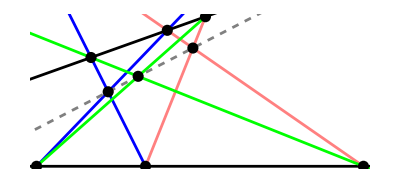

```mathematica
graphics[{{Directive[Black,PointSize[0.02]],a,b,c,d,e,f,xx,yy,zz},{Black,Thickness[0.005],line[a,b],line[d,e],Blue,line[a,e],line[b,d],Pink,line[b,f],line[e,c],Green,line[d,c],line[a,f],Gray,Dashed,line[xx,yy]}}/.{AA->0,BB->1,CC->3,x1->0.5,y1->1,x2->1.2,y2->1.25,k->1.5}//Evaluate]
```

### 2

-Graphics-

```mathematica
Clear[cir,qq,rr,pp,l1,l2,aa,bb,cc,dd,AD,BC,xx];
```

```mathematica
cir=circle[point[0,0],r];pp=point[0,h];
```

```mathematica
{qq,rr}=tangentpoint[pp,cir]
```

{point[…],point[…]}

```mathematica
l1=line[pp,arrow[k1,1]];l2=line[pp,arrow[k2,1]];
```

```mathematica
{aa,bb}=intersectpoint[l1,cir]//Simplify
```

{point[…],point[…]}

```mathematica
{cc,dd}=intersectpoint[l2,cir]//Simplify
```

{point[…],point[…]}

```mathematica
AD=line[aa,dd];BC=line[bb,cc];
```

```mathematica
xx=intersectpoint[AD,BC]//Simplify
```

point[…]

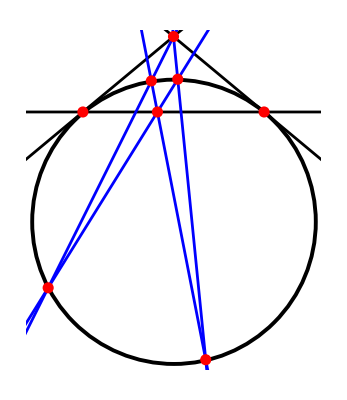

```mathematica
graphics[{{Thickness[0.007],Black,cir},{Directive[Red,PointSize[0.02]],pp,aa,bb,cc,dd,xx,qq,rr},{Black,Thickness[0.005],line[qq,rr],line[pp,qq],line[pp,rr],Blue,l1,l2,AD,BC}}/.{r->1,h->1.3,k1->0.5,k2->-0.1}]
```

### 3蝴蝶定理

```mathematica
Clear[cir,a,b,c,d,p,q,r,m,n,qr,ab,cd,ad,bc]
```

```mathematica
cir=circle[point[0,0],R];qr=line[point[0,H],arrow[1,0]];
```

```mathematica
{q,r}=intersectpoint[qr,cir]
```

{point[…],point[…]}

```mathematica
p=midpoint[q,r]
```

point[…]

```mathematica
ad=line[p,arrow[k1,1]];bc=line[p,arrow[k2,1]];
```

```mathematica
{a,d}=intersectpoint[ad,cir]//Simplify
```

{point[…],point[…]}

```mathematica
{c,b}=intersectpoint[bc,cir]//Simplify
```

{point[…],point[…]}

```mathematica
ab=line[a,b];cd=line[c,d];
```

```mathematica
m=intersectpoint[qr,ab]//Simplify
```

point[…]

```mathematica
n=intersectpoint[cd,qr]//Simplify
```

point[…]

```mathematica
midpoint[m,n]//Simplify
```

point[…]

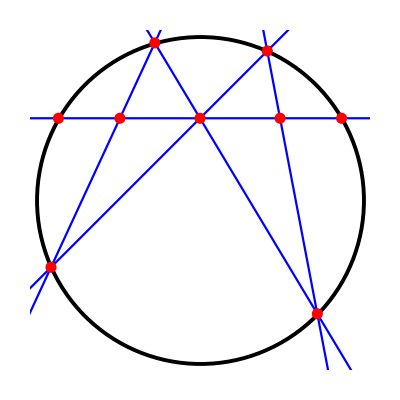

```mathematica
graphics[{Thickness[0.007],Black,cir,{Red,PointSize[0.02],a,b,c,d,p,q,r,m,n},Thickness[0.004],Blue,qr,ab,cd,ad,bc}/.{R->1,H->0.5,k1->1,k2->-0.6}]
```

### 4垂心

```mathematica
Clear[x1,y1,x2,y2,x3,y3]
```

```mathematica
a=point[x1,y1];b=point[x2,y2];c=point[x3,y3];
```

```mathematica
ah=verticalline[a,arrow[b,c]];bh=verticalline[b,arrow[a,c]];
```

```mathematica
h=intersectpoint[ah,bh]//Simplify
```

point[…]

### 5外心

```mathematica
a=point[x1,y1];b=point[x2,y2];c=point[x3,y3];
```

```mathematica
obc=midverticalline[b,c];oac=midverticalline[a,c];oab=midverticalline[a,b];
```

```mathematica
o=intersectpoint[oac,obc]
```

point[…]

```mathematica
oo=intersectpoint[oac,oab]
```

point[…]

### 6内心

```mathematica
a=point[x1,y1];b=point[x2,y2];c=point[x3,y3];
```

```mathematica
ab=arrow[a,b];ac=arrow[a,c];ao=midangle[ab,ac];lao=line[a,ao];
```

```mathematica
ba=arrow[b,a];bc=arrow[b,c];bo=midangle[ba,bc];lbc=line[b,bo];
```

```mathematica
lao
```

line[…]

```mathematica
intersectpoint[lao,lbc]//Simplify
```

point[…]

### 7旁心

```mathematica
a=point[x1,y1];b=point[x2,y2];c=point[x3,y3];
```

```mathematica
ab=arrow[a,b];ac=arrow[a,c];ai=midangle[ab,ac];lai=line[a,ai];
```

```mathematica
bc=arrow[b,c];bi=midangle[bc,ab];lbi=line[b,bi];
```

```mathematica
i=intersectpoint[lai,lbi]//Simplify
```

point[…]

### 8.欧拉线，九点圆

```mathematica
a=point[x1,y1];b=point[x2,y2];c=point[x3,y3];
```

```mathematica
o=circumcenter[a,b,c];h=orthocenter[a,b,c];g=centroid[a,b,c];
```

```mathematica
eul=eulerline[a,b,c]
```

line[…]

```mathematica
onlineQ[o,h,g]
```

True

```mathematica
onlineQ[o,eul]
```

True

```mathematica
Together/@arrow[o,h]//Simplify
```

arrow[…]

```mathematica
Together/@arrow[h,g]//Simplify
```

arrow[…]

```mathematica
Together/@arrow[o,g]//Simplify
```

arrow[…]

```mathematica
parallelQ[arrow[o,g],arrow[h,g]]
```

True

```mathematica
line[o,h]//Simplify
```

line[…]

```mathematica
onlineQ[point@@ninepointcircle[a,b,c][1],eul]
```

True

```mathematica
ninepointcircle[a,b,c]
```

circle[…]

### 9. tutorial/SyntheticGeometry 布拉马古普塔定理

-Graphics-

```mathematica
Clear[a,b,c,d,o,m,n]
```

```mathematica
o=point[0,0];a=point[0,AA];b=point[-BB,0];d=point[DD,0];cir=circle[a,b,d];
```

```mathematica
c=intersectpoint[cir,line[a,o]][[2]]
```

point[…]

```mathematica
mn=verticalline[o,arrow[c,d]]
```

line[…]

```mathematica
n=intersectpoint[mn,line[a,b]]
```

point[…]

### 10

-Graphics-

```mathematica
b=point[-AA,0];c=point[AA,0];a=point[x1,y1];
```

```mathematica
cir=circle[a,b,c];
```

```mathematica
d=intersectpoint[cir,line[c,arrow[k,1]]]//Last
```

point[…]

```mathematica
f=intersectpoint[line[a,d],line[b,c]]
```

point[…]

```mathematica
e=intersectpoint[line[a,b],line[c,d]]
```

point[…]

```mathematica
greatline[f,cir]
```

line[…]

```mathematica
onlineQ[greatline[f,cir],e]
```

True

```mathematica
{p,q}=tangentpoint[f,cir]
```

{point[…],point[…]}

```mathematica
onlineQ[p,q,e]
```

True

### 11

-Graphics-

```mathematica
Clear[l1,l2,l3,l4,a,b,c,d,e,f,g,r1,r2,k];
```

```mathematica
a=point[0,0];b=point[k,0];
```

```mathematica
cir1=circle[r1];cir2=circle[b,r2];
```

```mathematica
{l1,l2,l3,l4}=tangentline[cir1,cir2,4]
```

{line[…],line[…],line[…],line[…]}

```mathematica
c=intersectpoint[l1,l4]
```

point[…]

```mathematica
d=intersectpoint[l2,l3]
```

point[…]

```mathematica
g1=intersectpoint[line[c,d],line[a,b]]
```

point[…]

```mathematica
e=intersectpoint[cir2,l1]
```

point[…]

```mathematica
f=intersectpoint[cir2,l3]
```

point[…]

```mathematica
g2=intersectpoint[line[e,f],line[a,b]]//Simplify
```

point[…]

```mathematica
g1-g2//FullSimplify
```

point[…]

### 12 五点共圆：计算量有点大，慎用

-Graphics-

```mathematica
coord[x,y];
```

```mathematica
Clear[A,B,u,v];
```

```mathematica
Table[Subscript[A, i]=point[Subscript[u, i],Subscript[v, i]],{i,0,4}]
```

{point[…],point[…],point[…],point[…],point[…]}

```mathematica
Subscript[A, 0]=point[0,0];Subscript[A, 1]=point[Subscript[u, 1],0];(*选取坐标系，简化计算*)
```

```mathematica
Table[Subscript[B, i]=intersectpoint[line[Subscript[A, i],Subscript[A, Mod[i+1,5]]],line[Subscript[A, Mod[i+2,5]],Subscript[A, Mod[i+3,5]]]],{i,0,4}]
```

{point[…],point[…],point[…],point[…],point[…]}

```mathematica
Table[Subscript[cir, i]=circle[Subscript[B, i],Subscript[A, Mod[i+1,5]],Subscript[A, Mod[i+2,5]]],{i,0,4}]
```

{circle[…],circle[…],circle[…],circle[…],circle[…]}

```mathematica
Table[Subscript[CC, i]=intersectpoint[Subscript[cir, Mod[i+3,5]],Subscript[cir, Mod[i+4,5]],Subscript[A, i]]//Simplify,{i,0,4}]
```

{point[…],point[…],point[…],point[…],point[…]}

```mathematica
fivepointcircle=circle[Subscript[CC, 0],Subscript[CC, 1],Subscript[CC, 2]]
```

circle[…]

```mathematica
oncircle[Subscript[CC, 1],Subscript[CC, 2],Subscript[CC, 3],Subscript[CC, 4]]//Together
```

0

## craft

```mathematica
a=point[1,1];b=point[2,3];c=point[3,0];ab=line[a,b];cir=circle[a,b,c];
```

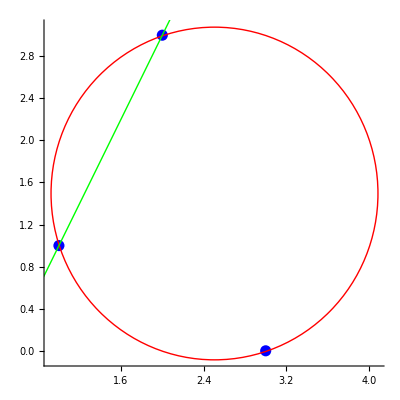

```mathematica
graphics[{Directive[Blue,PointSize[0.02]],a,b,c,Red,cir,Green,ab},Axes->True]
```

```mathematica
a=arrow[x1,y1];b=arrow[x2,y2];c=t a+(1-t)b;
```

```mathematica
cosangle[a,c]
```

(x1 x2+t (x1^2-x1 x2+y1 (y1-y2))+y1 y2)/(√(x1^2+y1^2) √((t (x1-x2)+x2)^2+(t (y1-y2)+y2)^2))

```mathematica
cosangle[b,c]
```

(x2^2+y2^2+t (x1 x2-x2^2+(y1-y2) y2))/(√(x2^2+y2^2) √((t (x1-x2)+x2)^2+(t (y1-y2)+y2)^2))